```mathematica
SetOptions[Graphics,BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];

SetOptions[{Plot,ListPlot,ParametricPlot},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
```

# Set - Up

## Trade - offs

```mathematica
(* Baseline transformed traits (no care)*)
muStar[params_]:=(θ/. params);
rStar[params_]:=(s*Exp[-(1-θ)])/. params;
nuStar[params_]:=(1-(1-ν0)*Exp[-(1-θ)])/. params;
sigmaJStar[params_]:=(1-(1-σJ0)*Exp[-(1-θ)])/. params;

(* Exponential trade-off*)
tradeOff["Exp"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*Exp[-a*c],r0*Exp[-c],1-(1-nu0b)*Exp[-c],1-(1-sigmaJ0b)*Exp[-a*c]}/. params];

(* Saturating trade-off*)
tradeOff["Saturating"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,V=0.9,Khalf=0.3,sigmaJMax=0.9,costR=0.8,costNu=0.8},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*(1-(V*c)/(Khalf+c)),r0*Exp[-costR*c],1-(1-nu0b)*Exp[-costNu*c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*(c/(Khalf+c))}/. params];

(* Sigmoid trade-off*)
tradeOff["Sigmoid"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,k=10.,c0=0.3,sigmaJMax=1,L,L0,Lnorm},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
L[x_]:=1/(1+Exp[-k*(x-c0)]);
L0=L[0];
Lnorm[x_]:=(L[x]-L0)/(1-L0);
{mu0*(1-L[c]),r0*Exp[-c],1-(1-nu0b)*Exp[-c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*Lnorm[c]}/. params];
```

## Optimal Parameters

```mathematica
(*Optimal parameters *)
baseParamsAdult={θ->0.8,σJ0->0.323823,s->6.,mE->0.2,K->250,a->6};

meanNu=0.1;
careVals=Range[0,2,0.02];
```

## Distribution

```mathematica
adultMortalityDist[mean_,kappa_]:=Module[{alpha,beta},alpha=mean*kappa;
beta=(1-mean)*kappa;
BetaDistribution[alpha,beta]];
```

## Functions

```mathematica
getFitFixedC[params_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:fixed care c=0.5*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,0.5];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V]

getFitAtC[params_,c_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:care=c*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V]
```

## Big Function

```mathematica
runAdultMortalityCase[kappa_,n_,seed_,shape_String:"Exp"]:=Module[
{nuVals,(*sampled adult mortality values*)
paramSets,(*full parameter sets with different mortality values*)
fitnessFixedC,(*invasion fitness at fixed care c=0.5*)
resultsFixedC,(*paired (adult mortality x fitness) values*)
fitnessByCare,(*invasion fitness across all care levels*)
meanByCare,(*mean fitness across care*)
sdByCare         (*standard deviation of fitness across care*)},

(*fix seed*)
SeedRandom[seed];


nuVals=RandomVariate[adultMortalityDist[meanNu,kappa],n];

Print[Histogram[nuVals,20,AxesLabel->{"Adult mortality (ν)","Frequency"},PlotLabel->"Adult mortality distribution ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];


paramSets=Table[Join[baseParamsAdult,{ν0->nu}],{nu,nuVals}];


fitnessFixedC=Table[getFitFixedC[paramSets[[i]],shape],{i,Length[paramSets]}];


resultsFixedC=Transpose[{nuVals,fitnessFixedC}];

Print[ListPlot[resultsFixedC,AxesLabel->{"Adult mortality (ν)","Fitness (λ)"},PlotRange->All,PlotLabel->"Fitness vs adult mortality ("<>shape<>", c = 0.5, κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];


fitnessByCare=Table[{c,Table[getFitAtC[paramSets[[i]],c,shape],{i,Length[paramSets]}]},{c,careVals}];


meanByCare={#[[1]],Mean[#[[2]]]}&/@fitnessByCare;


sdByCare={#[[1]],StandardDeviation[#[[2]]]}&/@fitnessByCare;

(*plot mean invasion fitness as a function of care*)Print[ListPlot[meanByCare,Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotRange->All,PlotLabel->"Mean fitness vs care ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*plot standard deviation of invasion fitness as a function of care*)Print[ListPlot[sdByCare,Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotRange->All,PlotLabel->"SD of fitness vs care ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];


{meanByCare,sdByCare}];
```

# Exponential

## Bulk Code

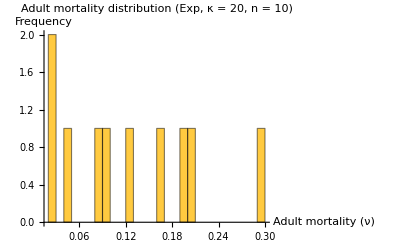

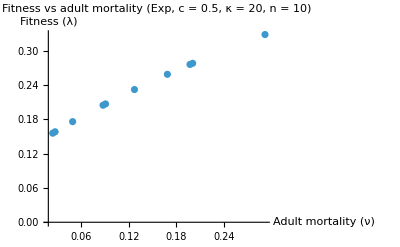

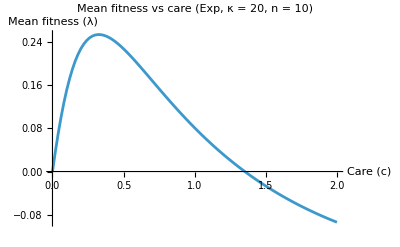

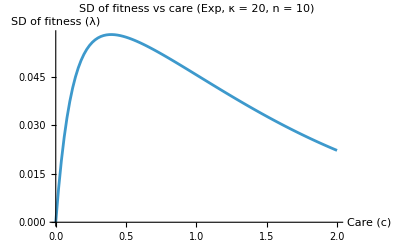

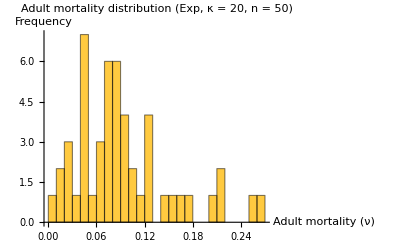

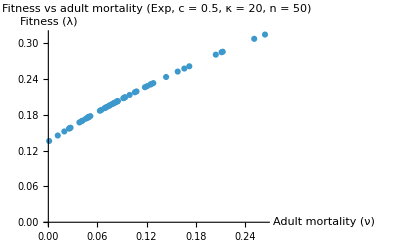

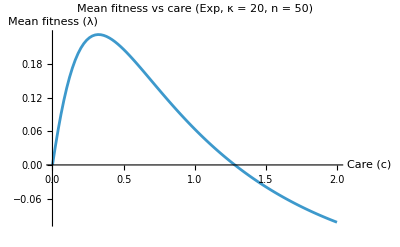

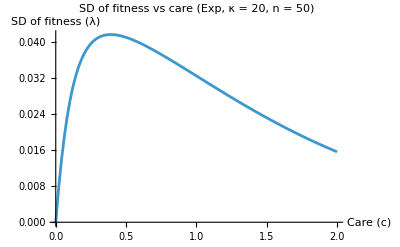

```mathematica
{meanFitnessByCareA10Exp,sdFitnessByCareA10Exp}=runAdultMortalityCase[20,10,2010,"Exp"];

{meanFitnessByCareA50Exp,sdFitnessByCareA50Exp}=runAdultMortalityCase[20,50,2050,"Exp"];

{meanFitnessByCareA100Exp,sdFitnessByCareA100Exp}=runAdultMortalityCase[20,100,2100,"Exp"];


{meanFitnessByCareB10Exp,sdFitnessByCareB10Exp}=runAdultMortalityCase[10,10,1010,"Exp"];

{meanFitnessByCareB50Exp,sdFitnessByCareB50Exp}=runAdultMortalityCase[10,50,1050,"Exp"];

{meanFitnessByCareB100Exp,sdFitnessByCareB100Exp}=runAdultMortalityCase[10,100,1100,"Exp"];


{meanFitnessByCareC10Exp,sdFitnessByCareC10Exp}=runAdultMortalityCase[30,10,3010,"Exp"];

{meanFitnessByCareC50Exp,sdFitnessByCareC50Exp}=runAdultMortalityCase[30,50,3050,"Exp"];

{meanFitnessByCareC100Exp,sdFitnessByCareC100Exp}=runAdultMortalityCase[30,100,3100,"Exp"];
```

## Diagnostic Plots

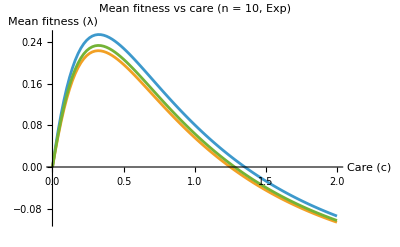

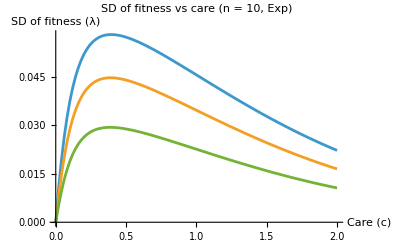

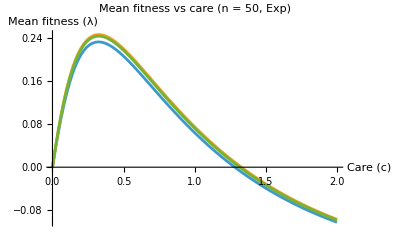

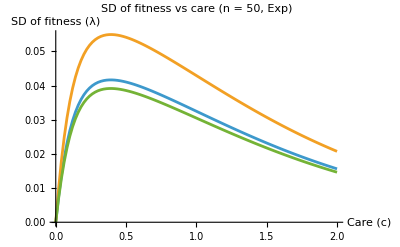

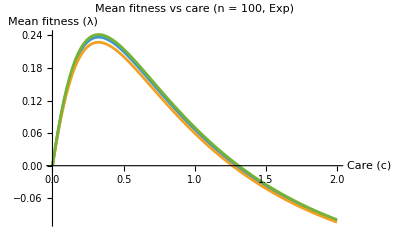

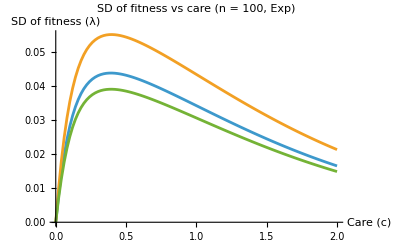

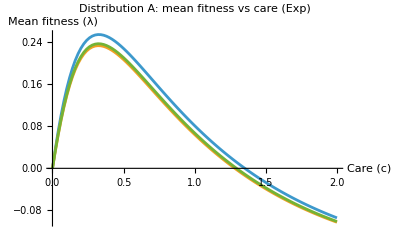

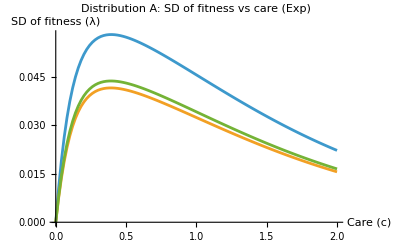

```mathematica
(*Grouped by sample size*)

ListPlot[{meanFitnessByCareA10Exp,meanFitnessByCareB10Exp,meanFitnessByCareC10Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Mean fitness vs care (n = 10, Exp)"]

ListPlot[{sdFitnessByCareA10Exp,sdFitnessByCareB10Exp,sdFitnessByCareC10Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"SD of fitness vs care (n = 10, Exp)"]


ListPlot[{meanFitnessByCareA50Exp,meanFitnessByCareB50Exp,meanFitnessByCareC50Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Mean fitness vs care (n = 50, Exp)"]

ListPlot[{sdFitnessByCareA50Exp,sdFitnessByCareB50Exp,sdFitnessByCareC50Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"SD of fitness vs care (n = 50, Exp)"]


ListPlot[{meanFitnessByCareA100Exp,meanFitnessByCareB100Exp,meanFitnessByCareC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Mean fitness vs care (n = 100, Exp)"]

ListPlot[{sdFitnessByCareA100Exp,sdFitnessByCareB100Exp,sdFitnessByCareC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"SD of fitness vs care (n = 100, Exp)"]



(*Grouped by distribution*)

ListPlot[{meanFitnessByCareA10Exp,meanFitnessByCareA50Exp,meanFitnessByCareA100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Distribution A: mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareA10Exp,sdFitnessByCareA50Exp,sdFitnessByCareA100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Distribution A: SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareB10Exp,meanFitnessByCareB50Exp,meanFitnessByCareB100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Distribution B: mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareB10Exp,sdFitnessByCareB50Exp,sdFitnessByCareB100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Distribution B: SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareC10Exp,meanFitnessByCareC50Exp,meanFitnessByCareC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Distribution C: mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareC10Exp,sdFitnessByCareC50Exp,sdFitnessByCareC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Distribution C: SD of fitness vs care (Exp)"]
```

## Tables

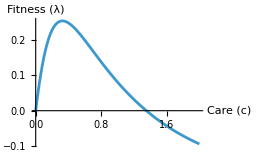
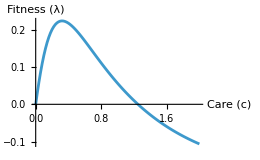
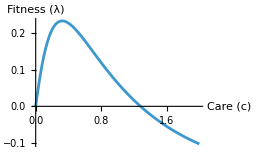
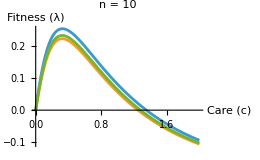
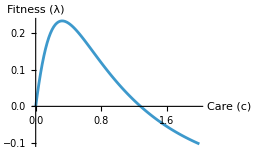
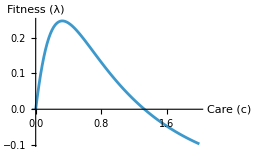
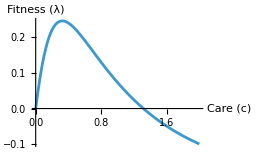
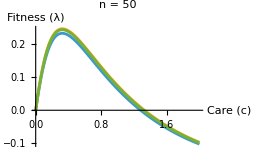
Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

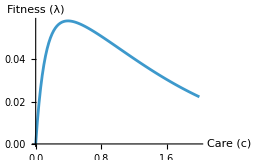
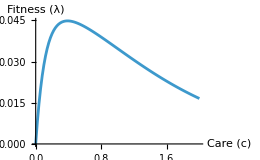
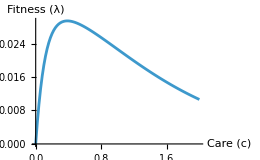
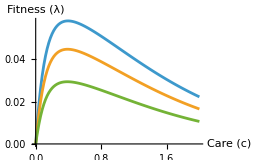
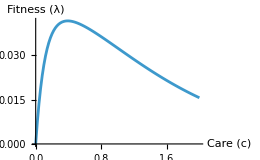
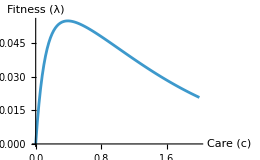
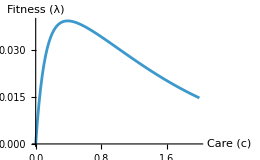
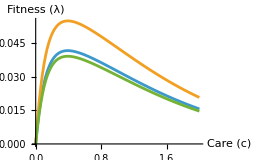
SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
plotOpts={Joined->True,PlotRange->All,AxesLabel->{"Care (c)","Fitness (λ)"},ImageSize->260};
meanA10Exp=ListPlot[{meanFitnessByCareA10Exp,meanFitnessByCareB10Exp,meanFitnessByCareC10Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanA50Exp=ListPlot[{meanFitnessByCareA50Exp,meanFitnessByCareB50Exp,meanFitnessByCareC50Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanA100Exp=ListPlot[{meanFitnessByCareA100Exp,meanFitnessByCareB100Exp,meanFitnessByCareC100Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanCompAExp=ListPlot[{meanFitnessByCareA10Exp,meanFitnessByCareA50Exp,meanFitnessByCareA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanCompBExp=ListPlot[{meanFitnessByCareB10Exp,meanFitnessByCareB50Exp,meanFitnessByCareB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanCompCExp=ListPlot[{meanFitnessByCareC10Exp,meanFitnessByCareC50Exp,meanFitnessByCareC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableAdultExp=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareA10Exp},plotOpts],ListPlot[{meanFitnessByCareB10Exp},plotOpts],ListPlot[{meanFitnessByCareC10Exp},plotOpts],meanA10Exp},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareA50Exp},plotOpts],ListPlot[{meanFitnessByCareB50Exp},plotOpts],ListPlot[{meanFitnessByCareC50Exp},plotOpts],meanA50Exp},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareA100Exp},plotOpts],ListPlot[{meanFitnessByCareB100Exp},plotOpts],ListPlot[{meanFitnessByCareC100Exp},plotOpts],meanA100Exp},{Style["Compiled",Bold],meanCompAExp,meanCompBExp,meanCompCExp,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableAdultExp=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareA10Exp},plotOpts],ListPlot[{sdFitnessByCareB10Exp},plotOpts],ListPlot[{sdFitnessByCareC10Exp},plotOpts],ListPlot[{sdFitnessByCareA10Exp,sdFitnessByCareB10Exp,sdFitnessByCareC10Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareA50Exp},plotOpts],ListPlot[{sdFitnessByCareB50Exp},plotOpts],ListPlot[{sdFitnessByCareC50Exp},plotOpts],ListPlot[{sdFitnessByCareA50Exp,sdFitnessByCareB50Exp,sdFitnessByCareC50Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareA100Exp},plotOpts],ListPlot[{sdFitnessByCareB100Exp},plotOpts],ListPlot[{sdFitnessByCareC100Exp},plotOpts],ListPlot[{sdFitnessByCareA100Exp,sdFitnessByCareB100Exp,sdFitnessByCareC100Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareA10Exp,sdFitnessByCareA50Exp,sdFitnessByCareA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareB10Exp,sdFitnessByCareB50Exp,sdFitnessByCareB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareC10Exp,sdFitnessByCareC50Exp,sdFitnessByCareC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableAdultExp
sdTableAdultExp
```

## Big Plots

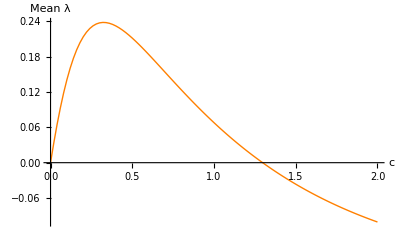

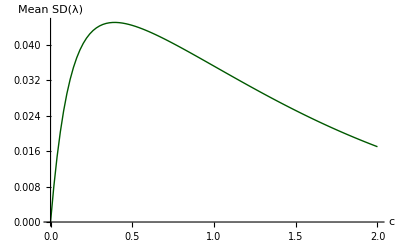

```mathematica
allMeanCurvesAExp={meanFitnessByCareA10Exp,meanFitnessByCareA50Exp,meanFitnessByCareA100Exp,meanFitnessByCareB10Exp,meanFitnessByCareB50Exp,meanFitnessByCareB100Exp,meanFitnessByCareC10Exp,meanFitnessByCareC50Exp,meanFitnessByCareC100Exp};

allSDCurvesAExp={sdFitnessByCareA10Exp,sdFitnessByCareA50Exp,sdFitnessByCareA100Exp,sdFitnessByCareB10Exp,sdFitnessByCareB50Exp,sdFitnessByCareB100Exp,sdFitnessByCareC10Exp,sdFitnessByCareC50Exp,sdFitnessByCareC100Exp};

careValuesAExp=allMeanCurvesAExp[[1]][[All,1]];

overallMeanAExp=Transpose[{careValuesAExp,Mean/@Transpose[allMeanCurvesAExp[[All,All,2]]]}];

overallSDAExp=Transpose[{careValuesAExp,Mean/@Transpose[allSDCurvesAExp[[All,All,2]]]}];

plotOverallMeanAExp=ListPlot[overallMeanAExp,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];

plotOverallSDAExp=ListPlot[overallSDAExp,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanAExp
plotOverallSDAExp
```

# Saturating

## Bulk Code

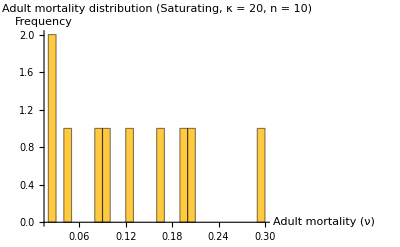

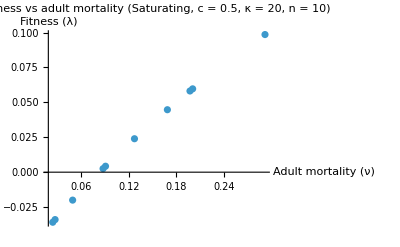

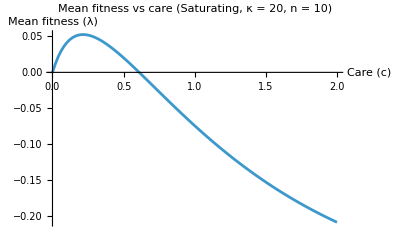

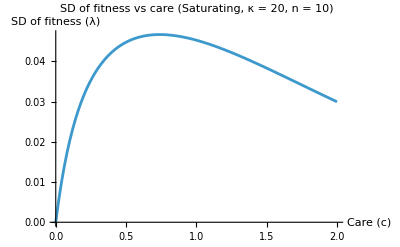

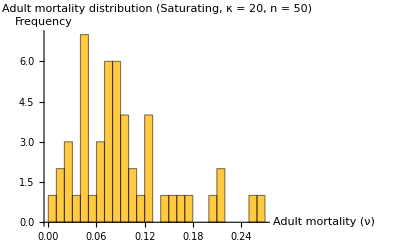

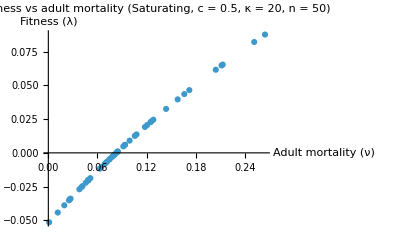

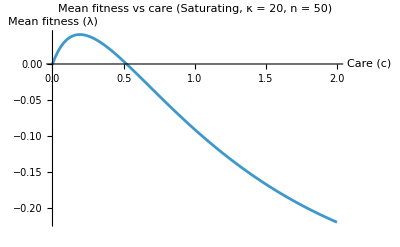

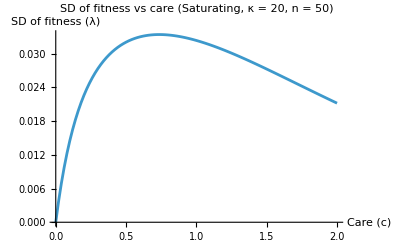

```mathematica
{meanFitnessByCareA10Sat,sdFitnessByCareA10Sat}=runAdultMortalityCase[20,10,2010,"Saturating"];

{meanFitnessByCareA50Sat,sdFitnessByCareA50Sat}=runAdultMortalityCase[20,50,2050,"Saturating"];

{meanFitnessByCareA100Sat,sdFitnessByCareA100Sat}=runAdultMortalityCase[20,100,2100,"Saturating"];


{meanFitnessByCareB10Sat,sdFitnessByCareB10Sat}=runAdultMortalityCase[10,10,1010,"Saturating"];

{meanFitnessByCareB50Sat,sdFitnessByCareB50Sat}=runAdultMortalityCase[10,50,1050,"Saturating"];

{meanFitnessByCareB100Sat,sdFitnessByCareB100Sat}=runAdultMortalityCase[10,100,1100,"Saturating"];


{meanFitnessByCareC10Sat,sdFitnessByCareC10Sat}=runAdultMortalityCase[30,10,3010,"Saturating"];

{meanFitnessByCareC50Sat,sdFitnessByCareC50Sat}=runAdultMortalityCase[30,50,3050,"Saturating"];

{meanFitnessByCareC100Sat,sdFitnessByCareC100Sat}=runAdultMortalityCase[30,100,3100,"Saturating"];
```

## Diagnostic Plots

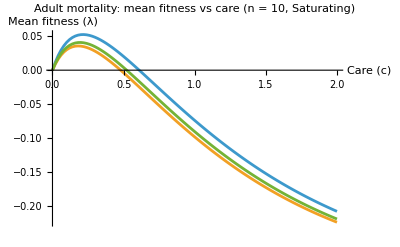

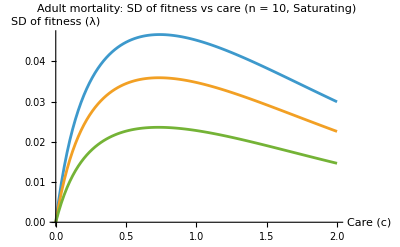

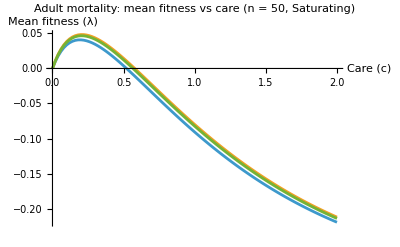

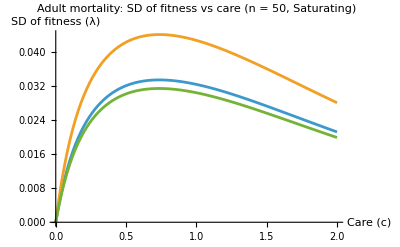

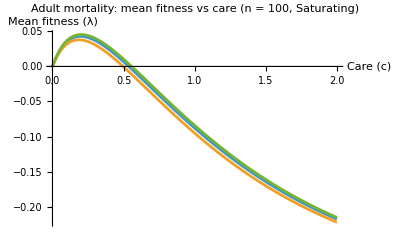

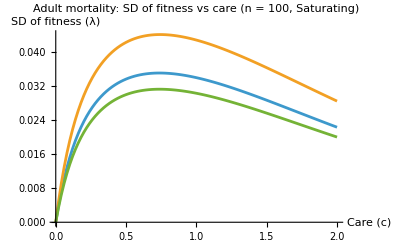

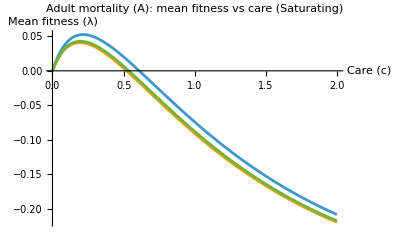

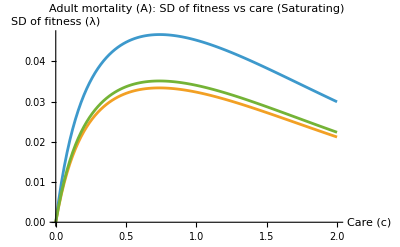

```mathematica
(*Grouped by sample size*)

ListPlot[{meanFitnessByCareA10Sat,meanFitnessByCareB10Sat,meanFitnessByCareC10Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: mean fitness vs care (n = 10, Saturating)"]

ListPlot[{sdFitnessByCareA10Sat,sdFitnessByCareB10Sat,sdFitnessByCareC10Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: SD of fitness vs care (n = 10, Saturating)"]


ListPlot[{meanFitnessByCareA50Sat,meanFitnessByCareB50Sat,meanFitnessByCareC50Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: mean fitness vs care (n = 50, Saturating)"]

ListPlot[{sdFitnessByCareA50Sat,sdFitnessByCareB50Sat,sdFitnessByCareC50Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: SD of fitness vs care (n = 50, Saturating)"]


ListPlot[{meanFitnessByCareA100Sat,meanFitnessByCareB100Sat,meanFitnessByCareC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: mean fitness vs care (n = 100, Saturating)"]

ListPlot[{sdFitnessByCareA100Sat,sdFitnessByCareB100Sat,sdFitnessByCareC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: SD of fitness vs care (n = 100, Saturating)"]

(*Grouped by distribution*)

ListPlot[{meanFitnessByCareA10Sat,meanFitnessByCareA50Sat,meanFitnessByCareA100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (A): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareA10Sat,sdFitnessByCareA50Sat,sdFitnessByCareA100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (A): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareB10Sat,meanFitnessByCareB50Sat,meanFitnessByCareB100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (B): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareB10Sat,sdFitnessByCareB50Sat,sdFitnessByCareB100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (B): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareC10Sat,meanFitnessByCareC50Sat,meanFitnessByCareC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (C): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareC10Sat,sdFitnessByCareC50Sat,sdFitnessByCareC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (C): SD of fitness vs care (Saturating)"]
```

## Tables

```mathematica
meanA10Sat=ListPlot[{meanFitnessByCareA10Sat,meanFitnessByCareB10Sat,meanFitnessByCareC10Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanA50Sat=ListPlot[{meanFitnessByCareA50Sat,meanFitnessByCareB50Sat,meanFitnessByCareC50Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanA100Sat=ListPlot[{meanFitnessByCareA100Sat,meanFitnessByCareB100Sat,meanFitnessByCareC100Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanCompASat=ListPlot[{meanFitnessByCareA10Sat,meanFitnessByCareA50Sat,meanFitnessByCareA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanCompBSat=ListPlot[{meanFitnessByCareB10Sat,meanFitnessByCareB50Sat,meanFitnessByCareB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanCompCSat=ListPlot[{meanFitnessByCareC10Sat,meanFitnessByCareC50Sat,meanFitnessByCareC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableAdultSat=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareA10Sat},plotOpts],ListPlot[{meanFitnessByCareB10Sat},plotOpts],ListPlot[{meanFitnessByCareC10Sat},plotOpts],meanA10Sat},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareA50Sat},plotOpts],ListPlot[{meanFitnessByCareB50Sat},plotOpts],ListPlot[{meanFitnessByCareC50Sat},plotOpts],meanA50Sat},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareA100Sat},plotOpts],ListPlot[{meanFitnessByCareB100Sat},plotOpts],ListPlot[{meanFitnessByCareC100Sat},plotOpts],meanA100Sat},{Style["Compiled",Bold],meanCompASat,meanCompBSat,meanCompCSat,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableAdultSat=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareA10Sat},plotOpts],ListPlot[{sdFitnessByCareB10Sat},plotOpts],ListPlot[{sdFitnessByCareC10Sat},plotOpts],ListPlot[{sdFitnessByCareA10Sat,sdFitnessByCareB10Sat,sdFitnessByCareC10Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareA50Sat},plotOpts],ListPlot[{sdFitnessByCareB50Sat},plotOpts],ListPlot[{sdFitnessByCareC50Sat},plotOpts],ListPlot[{sdFitnessByCareA50Sat,sdFitnessByCareB50Sat,sdFitnessByCareC50Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareA100Sat},plotOpts],ListPlot[{sdFitnessByCareB100Sat},plotOpts],ListPlot[{sdFitnessByCareC100Sat},plotOpts],ListPlot[{sdFitnessByCareA100Sat,sdFitnessByCareB100Sat,sdFitnessByCareC100Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareA10Sat,sdFitnessByCareA50Sat,sdFitnessByCareA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareB10Sat,sdFitnessByCareB50Sat,sdFitnessByCareB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareC10Sat,sdFitnessByCareC50Sat,sdFitnessByCareC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableAdultSat
sdTableAdultSat
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Big Plots

```mathematica
allMeanCurvesASat={meanFitnessByCareA10Sat,meanFitnessByCareA50Sat,meanFitnessByCareA100Sat,meanFitnessByCareB10Sat,meanFitnessByCareB50Sat,meanFitnessByCareB100Sat,meanFitnessByCareC10Sat,meanFitnessByCareC50Sat,meanFitnessByCareC100Sat};

allSDCurvesASat={sdFitnessByCareA10Sat,sdFitnessByCareA50Sat,sdFitnessByCareA100Sat,sdFitnessByCareB10Sat,sdFitnessByCareB50Sat,sdFitnessByCareB100Sat,sdFitnessByCareC10Sat,sdFitnessByCareC50Sat,sdFitnessByCareC100Sat};

careValuesASat=allMeanCurvesASat[[1]][[All,1]];

overallMeanASat=Transpose[{careValuesASat,Mean/@Transpose[allMeanCurvesASat[[All,All,2]]]}];

overallSDASat=Transpose[{careValuesASat,Mean/@Transpose[allSDCurvesASat[[All,All,2]]]}];

(*Mean*)
plotOverallMeanASat=ListPlot[overallMeanASat,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];

(*SD*)
plotOverallSDASat=ListPlot[overallSDASat,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanASat
plotOverallSDASat
```

-Graphics-

-Graphics-

# Sigmoid

## Bulk Code

```mathematica
{meanFitnessByCareA10Sig,sdFitnessByCareA10Sig}=runAdultMortalityCase[20,10,2010,"Sigmoid"];

{meanFitnessByCareA50Sig,sdFitnessByCareA50Sig}=runAdultMortalityCase[20,50,2050,"Sigmoid"];

{meanFitnessByCareA100Sig,sdFitnessByCareA100Sig}=runAdultMortalityCase[20,100,2100,"Sigmoid"];


{meanFitnessByCareB10Sig,sdFitnessByCareB10Sig}=runAdultMortalityCase[10,10,1010,"Sigmoid"];

{meanFitnessByCareB50Sig,sdFitnessByCareB50Sig}=runAdultMortalityCase[10,50,1050,"Sigmoid"];

{meanFitnessByCareB100Sig,sdFitnessByCareB100Sig}=runAdultMortalityCase[10,100,1100,"Sigmoid"];


{meanFitnessByCareC10Sig,sdFitnessByCareC10Sig}=runAdultMortalityCase[30,10,3010,"Sigmoid"];

{meanFitnessByCareC50Sig,sdFitnessByCareC50Sig}=runAdultMortalityCase[30,50,3050,"Sigmoid"];

{meanFitnessByCareC100Sig,sdFitnessByCareC100Sig}=runAdultMortalityCase[30,100,3100,"Sigmoid"];
```

-Graphics-

-Graphics-

-Graphics-

«33 more identical outputs»

## Diagnostic Plots

```mathematica
(*Grouped by sample size*)

ListPlot[{meanFitnessByCareA10Sig,meanFitnessByCareB10Sig,meanFitnessByCareC10Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: mean fitness vs care (n = 10, Sigmoid)"]

ListPlot[{sdFitnessByCareA10Sig,sdFitnessByCareB10Sig,sdFitnessByCareC10Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: SD of fitness vs care (n = 10, Sigmoid)"]


ListPlot[{meanFitnessByCareA50Sig,meanFitnessByCareB50Sig,meanFitnessByCareC50Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: mean fitness vs care (n = 50, Sigmoid)"]

ListPlot[{sdFitnessByCareA50Sig,sdFitnessByCareB50Sig,sdFitnessByCareC50Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: SD of fitness vs care (n = 50, Sigmoid)"]


ListPlot[{meanFitnessByCareA100Sig,meanFitnessByCareB100Sig,meanFitnessByCareC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: mean fitness vs care (n = 100, Sigmoid)"]

ListPlot[{sdFitnessByCareA100Sig,sdFitnessByCareB100Sig,sdFitnessByCareC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Adult mortality: SD of fitness vs care (n = 100, Sigmoid)"]

(*Grouped by distribution*)

ListPlot[{meanFitnessByCareA10Sig,meanFitnessByCareA50Sig,meanFitnessByCareA100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (A): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareA10Sig,sdFitnessByCareA50Sig,sdFitnessByCareA100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (A): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareB10Sig,meanFitnessByCareB50Sig,meanFitnessByCareB100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (B): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareB10Sig,sdFitnessByCareB50Sig,sdFitnessByCareB100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (B): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareC10Sig,meanFitnessByCareC50Sig,meanFitnessByCareC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (C): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareC10Sig,sdFitnessByCareC50Sig,sdFitnessByCareC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Adult mortality (C): SD of fitness vs care (Sigmoid)"]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

## Tables

```mathematica
meanA10Sig=ListPlot[{meanFitnessByCareA10Sig,meanFitnessByCareB10Sig,meanFitnessByCareC10Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanA50Sig=ListPlot[{meanFitnessByCareA50Sig,meanFitnessByCareB50Sig,meanFitnessByCareC50Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanA100Sig=ListPlot[{meanFitnessByCareA100Sig,meanFitnessByCareB100Sig,meanFitnessByCareC100Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanCompASig=ListPlot[{meanFitnessByCareA10Sig,meanFitnessByCareA50Sig,meanFitnessByCareA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanCompBSig=ListPlot[{meanFitnessByCareB10Sig,meanFitnessByCareB50Sig,meanFitnessByCareB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanCompCSig=ListPlot[{meanFitnessByCareC10Sig,meanFitnessByCareC50Sig,meanFitnessByCareC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableAdultSig=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareA10Sig},plotOpts],ListPlot[{meanFitnessByCareB10Sig},plotOpts],ListPlot[{meanFitnessByCareC10Sig},plotOpts],meanA10Sig},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareA50Sig},plotOpts],ListPlot[{meanFitnessByCareB50Sig},plotOpts],ListPlot[{meanFitnessByCareC50Sig},plotOpts],meanA50Sig},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareA100Sig},plotOpts],ListPlot[{meanFitnessByCareB100Sig},plotOpts],ListPlot[{meanFitnessByCareC100Sig},plotOpts],meanA100Sig},{Style["Compiled",Bold],meanCompASig,meanCompBSig,meanCompCSig,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableAdultSig=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareA10Sig},plotOpts],ListPlot[{sdFitnessByCareB10Sig},plotOpts],ListPlot[{sdFitnessByCareC10Sig},plotOpts],ListPlot[{sdFitnessByCareA10Sig,sdFitnessByCareB10Sig,sdFitnessByCareC10Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareA50Sig},plotOpts],ListPlot[{sdFitnessByCareB50Sig},plotOpts],ListPlot[{sdFitnessByCareC50Sig},plotOpts],ListPlot[{sdFitnessByCareA50Sig,sdFitnessByCareB50Sig,sdFitnessByCareC50Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareA100Sig},plotOpts],ListPlot[{sdFitnessByCareB100Sig},plotOpts],ListPlot[{sdFitnessByCareC100Sig},plotOpts],ListPlot[{sdFitnessByCareA100Sig,sdFitnessByCareB100Sig,sdFitnessByCareC100Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareA10Sig,sdFitnessByCareA50Sig,sdFitnessByCareA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareB10Sig,sdFitnessByCareB50Sig,sdFitnessByCareB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareC10Sig,sdFitnessByCareC50Sig,sdFitnessByCareC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableAdultSig
sdTableAdultSig
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Big Plots

```mathematica
allMeanCurvesASig={meanFitnessByCareA10Sig,meanFitnessByCareA50Sig,meanFitnessByCareA100Sig,meanFitnessByCareB10Sig,meanFitnessByCareB50Sig,meanFitnessByCareB100Sig,meanFitnessByCareC10Sig,meanFitnessByCareC50Sig,meanFitnessByCareC100Sig};

allSDCurvesASig={sdFitnessByCareA10Sig,sdFitnessByCareA50Sig,sdFitnessByCareA100Sig,sdFitnessByCareB10Sig,sdFitnessByCareB50Sig,sdFitnessByCareB100Sig,sdFitnessByCareC10Sig,sdFitnessByCareC50Sig,sdFitnessByCareC100Sig};

careValuesASig=allMeanCurvesASig[[1]][[All,1]];

overallMeanASig=Transpose[{careValuesASig,Mean/@Transpose[allMeanCurvesASig[[All,All,2]]]}];

overallSDASig=Transpose[{careValuesASig,Mean/@Transpose[allSDCurvesASig[[All,All,2]]]}];

plotOverallMeanASig=ListPlot[overallMeanASig,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];

plotOverallSDASig=ListPlot[overallSDASig,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanASig
plotOverallSDASig
```

-Graphics-

-Graphics-

# Deterministic Shape

```mathematica
Aexpr[th_,v0_,sj_,ss_,me_,Kval_:250]:=Kval*(1-(((v0/sj)*(1+(th/me)))/ss));


(*Care mutant invading no-care resident*)
getFit[params_,shape_String:"Exp"]:=Module[
{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//Simplify;
Table[{val,Re[N[V/. c->val]]},{val,0,2,0.01}]];
```

```mathematica
params1={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};
params2={θ->0.7999967491603689,ν0->0.10000440803427434,σJ0->0.32383733876731385,s->5.999984154933559,mE->0.19999923208705223,K->250,a->6};
params3={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};

fit1=getFit[params1,"Exp"];
fit2=getFit[params2,"Saturating"];
fit3=getFit[params3,"Sigmoid"];

plotExp=ListPlot[fit1,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSaturating=ListPlot[fit2,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSigmoid=ListPlot[fit3,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];

plotExp
plotSaturating
plotSigmoid
```

-Graphics-

-Graphics-

-Graphics-

# SD Trends

```mathematica
imgW=520;
imgH=300;

meanStyle=Directive[Orange,Thick];
sdStyle=Directive[RGBColor[0,0.35,0],Thick];

extractXY[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];
First[d]];

makeMeanSDOverlayFromPlots[meanG_,sdG_,title_]:=Module[{meanData,sdData,xMin,xMax,meanMin,meanMax,sdMin,sdMax,meanPad,sdPad,meanPR,sdPR,scale,meanPlot,sdScaledPlot,sdTickVals,sdTickPos,sdTicksRight},meanData=extractXY[meanG];
sdData=extractXY[sdG];
xMin=Min[meanData[[All,1]]];
xMax=Max[meanData[[All,1]]];
meanMin=Min[meanData[[All,2]]];
meanMax=Max[meanData[[All,2]]];
sdMin=Min[sdData[[All,2]]];
sdMax=Max[sdData[[All,2]]];
meanPad=0.05*(meanMax-meanMin);If[meanPad==0,meanPad=0.1];
sdPad=0.05*(sdMax-sdMin);If[sdPad==0,sdPad=0.1];
meanPR={meanMin-meanPad,meanMax+meanPad};
sdPR={0,sdMax+sdPad};
scale[y_]:=Rescale[y,sdPR,meanPR];
meanPlot=ListPlot[meanData,Joined->True,PlotStyle->meanStyle,PlotRange->{{xMin,xMax},meanPR}];
sdScaledPlot=ListPlot[({#[[1]],scale[#[[2]]]}&/@sdData),Joined->True,PlotStyle->sdStyle,PlotRange->{{xMin,xMax},meanPR}];
sdTickVals=N@Subdivide[sdPR[[1]],sdPR[[2]],5];
sdTickPos=scale/@sdTickVals;
sdTicksRight=MapThread[{#1,NumberForm[#2,{Infinity,3}]}&,{sdTickPos,sdTickVals}];
Show[meanPlot,sdScaledPlot,ImageSize->{imgW,imgH},Frame->True,Axes->False,FrameLabel->{{"Mean λ","SD(λ)"},{"c",None}},FrameTicks->{{Automatic,sdTicksRight},{Automatic,None}},PlotLabel->Style[title,16]]];


adultExpMeanSD=makeMeanSDOverlayFromPlots[plotOverallMeanAExp,plotOverallSDAExp,"Exponential"];

adultSatMeanSD=makeMeanSDOverlayFromPlots[plotOverallMeanASat,plotOverallSDASat,"Saturating"];

adultSigMeanSD=makeMeanSDOverlayFromPlots[plotOverallMeanASig,plotOverallSDASig,"Sigmoid"];

figureLegend=LineLegend[{meanStyle,sdStyle},{"Mean λ","SD(λ)"},LegendLayout->"Row"];

adultMortalityMeanSDFigure=GraphicsGrid[{{Style["Adult Mortality",22,Bold,Underlined]},{figureLegend},{adultExpMeanSD},{adultSatMeanSD},{adultSigMeanSD}},Spacings->{2,1.5},Alignment->Center];

adultMortalityMeanSDFigure
```

-Graphics-

## Exponential Only

```mathematica
adultExpMeanSDwithLabel=Show[adultExpMeanSD,PlotLabel->None,(*removes "Exponential"*)Epilog->{Inset[Style["c)",16,Bold],Scaled[{0.5,0.9}]]}];

adultMortalityExpOnly=GraphicsColumn[{Style["Adult Mortality",22,Bold,Underlined],figureLegend,adultExpMeanSDwithLabel},Spacings->1.5,Alignment->Center];

adultMortalityExpOnly
```

-Graphics-

```mathematica
adultExpMeanSDStandalone=Show[adultExpMeanSD,PlotLabel->None,AxesLabel->{Style["c",20],Style["λ",20]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],ImageSize->500];

figureLegendAdultStandalone=LineLegend[{Directive[Orange,Thick],Directive[RGBColor[0,0.35,0],Thick]},{"Mean λ","SD(λ)"},LabelStyle->Directive[18,FontFamily->"Times New Roman"],LegendMarkerSize->35,LegendLayout->"Row"];

adultMortalityStandalone=GraphicsColumn[{figureLegendAdultStandalone,adultExpMeanSDStandalone},Spacings->1.5,Alignment->Center];

adultMortalityStandalone
```

-Graphics-

```mathematica
extractXY2[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];
First[d]];

makeMeanSDOverlayDashed[meanG_,sdG_,title_,panelLabel_]:=Module[{meanData,sdData,xMin,xMax,meanMin,meanMax,sdMin,sdMax,meanPad,sdPad,meanPR,sdPR,scale,meanPlot,sdScaledPlot,sdTickVals,sdTickPos,sdTicksRight,epilogContent},meanData=extractXY2[meanG];
sdData=extractXY2[sdG];
xMin=Min[meanData[[All,1]]];
xMax=Max[meanData[[All,1]]];
meanMin=Min[meanData[[All,2]]];
meanMax=Max[meanData[[All,2]]];
sdMin=Min[sdData[[All,2]]];
sdMax=Max[sdData[[All,2]]];
meanPad=0.05*(meanMax-meanMin);
If[meanPad==0,meanPad=0.1];
sdPad=0.05*(sdMax-sdMin);
If[sdPad==0,sdPad=0.1];
meanPR={meanMin-meanPad,meanMax+meanPad};
sdPR={0,sdMax+sdPad};
scale[y_]:=Rescale[y,sdPR,meanPR];
meanPlot=ListPlot[meanData,Joined->True,PlotStyle->Directive[Orange,Thick,Dashed],PlotRange->{{xMin,xMax},meanPR}];
sdScaledPlot=ListPlot[({#[[1]],scale[#[[2]]]}&/@sdData),Joined->True,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],PlotRange->{{xMin,xMax},meanPR}];
sdTickVals=N@Subdivide[sdPR[[1]],sdPR[[2]],5];
sdTickPos=scale/@sdTickVals;
sdTicksRight=MapThread[{#1,NumberForm[#2,{Infinity,3}]}&,{sdTickPos,sdTickVals}];
epilogContent=If[panelLabel===""||panelLabel===None,{},{Inset[Style["("<>panelLabel<>")",14,Bold],Scaled[{0.7,0.95}]]}];
Show[meanPlot,sdScaledPlot,ImageSize->{520,300},Frame->True,Axes->False,FrameLabel->{{Style["Mean λ",18],Style["SD(λ)",18]},{Style["c",20],None}},LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,sdTicksRight},{Automatic,None}},PlotLabel->None,Epilog->Join[epilogContent,{Inset[Style[Row[{"SD(λ*): 18.78%",Spacer[35],"|",Spacer[25],"Δ(c*-cSD): 0.0600"}],16],Scaled[{0.45,0.06}]]}]]];

figureLegendDashedBig=LineLegend[{Directive[Orange,Thick,Dashed],Directive[RGBColor[0,0.35,0],Thick]},{"Mean λ","SD(λ)"},LabelStyle->Directive[18,FontFamily->"Times New Roman"],LegendLayout->"Row"];

adultExpMeanSDNoLabel=makeMeanSDOverlayDashed[plotOverallMeanAExp,plotOverallSDAExp,"",""];

adultMortalityMeanSDExpOnly=GraphicsColumn[{figureLegendDashedBig,adultExpMeanSDNoLabel},Spacings->1.2,Alignment->Center];

adultMortalityMeanSDExpOnly
```

-Graphics-

## Metrics for SD

```mathematica
extractXY2[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];First[d]];

maxYFromPlot2[g_]:=Module[{xy=extractXY2[g]},Max[xy[[All,2]]]];

fmt4b[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];

adultMaxStats=Module[{shapes,meanPlots,sdPlots,rows},shapes={"Exponential","Saturating","Sigmoid"};
meanPlots={plotOverallMeanAExp,plotOverallMeanASat,plotOverallMeanASig};
sdPlots={plotOverallSDAExp,plotOverallSDASat,plotOverallSDASig};
rows=MapThread[Function[{shape,meanG,sdG},Module[{maxMean,maxSD,pct},maxMean=maxYFromPlot2[meanG];
maxSD=maxYFromPlot2[sdG];
pct=If[maxMean==0,Missing["Undefined"],100 maxSD/maxMean];
{shape,maxSD,maxMean,pct}]],{shapes,meanPlots,sdPlots}];
Grid[Prepend[(rows/. {s_,sd_,mn_,pc_}:>{s,fmt4b[sd],fmt4b[mn],fmt4b[pc]}),{"Trade-off shape","Max SD(λ)","Max Mean λ","Max SD as % of Max Mean"}],Frame->All,Alignment->Center,Background->{None,{Lighter[Gray,0.95],{White}}}]];

adultMaxStats
```

Trade-off shape | Max SD(λ) | Max Mean λ | Max SD as % of Max Mean
Exponential | 0.0451 | 0.2378 | 18.9723
Saturating | 0.0362 | 0.0434 | 83.2839
Sigmoid | 0.0422 | 0.1611 | 26.1680

```mathematica
extractXY2[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];First[d]];

fmt4[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];

interpAt[data_,x_]:=Interpolation[SortBy[data,First],InterpolationOrder->1][x];

adultCrossStatsFromPlots[meanG_,sdG_]:=Module[{meanData,sdData,maxSDPt,cAtMaxSD,sdMax,meanAtCmaxSD,pctSDofMeanAtMaxSD,maxMeanPt,cAtMaxMean,meanMax,sdAtCmaxMean,pctSDofMeanAtMaxMean},meanData=SortBy[extractXY2[meanG],First];
sdData=SortBy[extractXY2[sdG],First];

(*Max SD and the corresponding mean*)
maxSDPt=First@MaximalBy[sdData,Last];
cAtMaxSD=maxSDPt[[1]];
sdMax=maxSDPt[[2]];
meanAtCmaxSD=interpAt[meanData,cAtMaxSD];
pctSDofMeanAtMaxSD=100 sdMax/meanAtCmaxSD;

(*Max mean and the corresponding SD*)
maxMeanPt=First@MaximalBy[meanData,Last];
cAtMaxMean=maxMeanPt[[1]];
meanMax=maxMeanPt[[2]];
sdAtCmaxMean=interpAt[sdData,cAtMaxMean];
pctSDofMeanAtMaxMean=100 sdAtCmaxMean/meanMax;
<|"c at Max SD"->cAtMaxSD,"Max SD(λ)"->sdMax,"Mean λ at c(Max SD)"->meanAtCmaxSD,"Max SD as % of Mean λ at c(Max SD)"->pctSDofMeanAtMaxSD,"c at Max Mean λ"->cAtMaxMean,"Max Mean λ"->meanMax,"SD(λ) at c(Max Mean)"->sdAtCmaxMean,"SD at c(Max Mean) as % of Max Mean λ"->pctSDofMeanAtMaxMean|>];

adultStatsByShape={{"Exponential",adultCrossStatsFromPlots[plotOverallMeanAExp,plotOverallSDAExp]},{"Saturating",adultCrossStatsFromPlots[plotOverallMeanASat,plotOverallSDASat]},{"Sigmoid",adultCrossStatsFromPlots[plotOverallMeanASig,plotOverallSDASig]}};

adultCrossStatsTable=Grid[Prepend[({#[[1]],fmt4[#[[2]]["c at Max SD"]],fmt4[#[[2]]["Max SD(λ)"]],fmt4[#[[2]]["Mean λ at c(Max SD)"]],fmt4[#[[2]]["Max SD as % of Mean λ at c(Max SD)"]],fmt4[#[[2]]["c at Max Mean λ"]],fmt4[#[[2]]["Max Mean λ"]],fmt4[#[[2]]["SD(λ) at c(Max Mean)"]],fmt4[#[[2]]["SD at c(Max Mean) as % of Max Mean λ"]]}&/@adultStatsByShape),{"Trade-off shape","Care at Max SD","Max SD(λ)","Mean λ at that care","SD as % of Mean λ (at Max SD)","Care at Max Mean λ","Max Mean λ","SD at that care","SD as % of Max Mean λ (at Max Mean)"}],Frame->All,Alignment->Center,Background->{None,{Lighter[Gray,0.95],White}}];

adultCrossStatsTable
```

Trade-off shape | Care at Max SD | Max SD(λ) | Mean λ at that care | SD as % of Mean λ (at Max SD) | Care at Max Mean λ | Max Mean λ | SD at that care | SD as % of Max Mean λ (at Max Mean)
Exponential | 0.4000 | 0.0451 | 0.2318 | 19.4650 | 0.3200 | 0.2378 | 0.0447 | 18.7812
Saturating | 0.7400 | 0.0362 | -0.0385 | -93.8606 | 0.2000 | 0.0434 | 0.0244 | 56.2607
Sigmoid | 0.5200 | 0.0422 | 0.1578 | 26.7293 | 0.5600 | 0.1611 | 0.0421 | 26.1104

# Stochastic vs Deterministic Mean

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];

If[ValueQ[meanYRange]&&MatchQ[meanYRange,{_?NumericQ,_?NumericQ}],Null,If[And[ValueQ[overallMeanRExp],ValueQ[overallMeanRSat],ValueQ[overallMeanRSig],ValueQ[fit1],ValueQ[fit2],ValueQ[fit3]],allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],overallMeanRSat[[All,2]],overallMeanRSig[[All,2]],fit1[[All,2]],fit2[[All,2]],fit3[[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};,allMeanDetValues=Flatten[{getLineData[plotExp][[All,2]],getLineData[plotSaturating][[All,2]],getLineData[plotSigmoid][[All,2]],getLineData[plotOverallMeanAExp][[All,2]],getLineData[plotOverallMeanASat][[All,2]],getLineData[plotOverallMeanASig][[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};]];



(*exponential*)
detData=getLineData[plotExp];
stochData=getLineData[plotOverallMeanAExp];

detCol=getPlotColour[plotExp];
stochCol=getPlotColour[plotOverallMeanAExp];

exponentialOneEntityA=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Exponential",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];


(*saturating*)
detData=getLineData[plotSaturating];
stochData=getLineData[plotOverallMeanASat];

detCol=getPlotColour[plotSaturating];
stochCol=getPlotColour[plotOverallMeanASat];

saturatingOneEntityA=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Saturating",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];


(*sigmoid*)
detData=getLineData[plotSigmoid];
stochData=getLineData[plotOverallMeanASig];

detCol=getPlotColour[plotSigmoid];
stochCol=getPlotColour[plotOverallMeanASig];

sigmoidOneEntityA=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Sigmoid",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];

exponentialOneEntityA
saturatingOneEntityA
sigmoidOneEntityA
```

-Graphics-

-Graphics-

-Graphics-

## Exponential with Metrics

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];

If[ValueQ[meanYRange]&&MatchQ[meanYRange,{_?NumericQ,_?NumericQ}],Null,If[And[ValueQ[overallMeanRExp],ValueQ[fit1]],allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],fit1[[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean},allMeanDetValues=Flatten[{getLineData[plotExp][[All,2]],getLineData[plotOverallMeanAExp][[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean}]];



detData=getLineData[plotExp];
stochData=getLineData[plotOverallMeanAExp];

detCol=getPlotColour[plotExp];
stochCol=getPlotColour[plotOverallMeanAExp];

exponentialOneEntityA=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{Style["c",18],Style["λ",18]},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],ImageSize->500,Epilog->{Inset[Style[Row[{"Δ(c*) = 0.0000",Spacer[25],"|",Spacer[25],"Δ(λ*) = -0.0026",Spacer[25],"|",Spacer[25],"Δ(c₀) = -0.0051"}],20,FontFamily->"Times New Roman"],Scaled[{0.5,0.06}]]},PlotLabel->LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row",LabelStyle->Directive[20,FontFamily->"Times New Roman"]]];

exponentialOneEntityA
```

-Graphics-

## Metrics for Stochastic vs Deterministic Mean

```mathematica
ClearAll[getLineData,maxPointFromData,zeroCrossingsXNotOriginAll,firstZeroCrossingXNotOrigin,secondZeroCrossingXNotOrigin,diffRowForShape,formatNum,prettyResultsA,fmt,getRow,shapeTable,detExpData,stochExpData,detSatData,stochSatData,detSigData,stochSigData,resultsA,expTableA,satTableA,sigTableA];

getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];

maxPointFromData[data_]:=First@MaximalBy[data,Last];


zeroCrossingsXNotOriginAll[data_,tol_:10^-12]:=Module[{pts=SortBy[data,First],segs,roots},segs=Partition[pts,2,1];
roots=Reap[Do[With[{x1=seg[[1,1]],y1=seg[[1,2]],x2=seg[[2,1]],y2=seg[[2,2]]},If[Abs[y1]<=tol&&Abs[x1]>tol,Sow[x1]];
If[Abs[y2]<=tol&&Abs[x2]>tol,Sow[x2]];
If[y1*y2<0,With[{x0=x1-y1 (x2-x1)/(y2-y1)},If[Abs[x0]>tol,Sow[x0]]]];],{seg,segs}]][[2]];
If[roots==={}||roots==={{}},{},roots=DeleteDuplicates[First@roots,Abs[#1-#2]<10^-6&];
Sort@Select[roots,#>tol&]]];

firstZeroCrossingXNotOrigin[data_,tol_:10^-12]:=Module[{xs=zeroCrossingsXNotOriginAll[data,tol]},If[xs==={},Missing["NoPositiveZeroCrossing"],xs[[1]]]];

secondZeroCrossingXNotOrigin[data_,tol_:10^-12]:=Module[{xs=zeroCrossingsXNotOriginAll[data,tol]},If[Length[xs]<2,Missing["NoSecondZeroCrossing"],xs[[2]]]];


detExpData=getLineData[plotExp];
stochExpData=getLineData[plotOverallMeanAExp];

detSatData=getLineData[plotSaturating];
stochSatData=getLineData[plotOverallMeanASat];

detSigData=getLineData[plotSigmoid];
stochSigData=getLineData[plotOverallMeanASig];


resultsA={{"Exponential","Deterministic",maxPointFromData[detExpData],firstZeroCrossingXNotOrigin[detExpData],secondZeroCrossingXNotOrigin[detExpData]},{"Exponential","Stochastic",maxPointFromData[stochExpData],firstZeroCrossingXNotOrigin[stochExpData],secondZeroCrossingXNotOrigin[stochExpData]},{"Saturating","Deterministic",maxPointFromData[detSatData],firstZeroCrossingXNotOrigin[detSatData],secondZeroCrossingXNotOrigin[detSatData]},{"Saturating","Stochastic",maxPointFromData[stochSatData],firstZeroCrossingXNotOrigin[stochSatData],secondZeroCrossingXNotOrigin[stochSatData]},{"Sigmoid","Deterministic",maxPointFromData[detSigData],firstZeroCrossingXNotOrigin[detSigData],secondZeroCrossingXNotOrigin[detSigData]},{"Sigmoid","Stochastic",maxPointFromData[stochSigData],firstZeroCrossingXNotOrigin[stochSigData],secondZeroCrossingXNotOrigin[stochSigData]}};


diffRowForShape[shape_]:=Module[{det,stoch},det=SelectFirst[resultsA,#[[1]]==shape&&#[[2]]=="Deterministic"&];
stoch=SelectFirst[resultsA,#[[1]]==shape&&#[[2]]=="Stochastic"&];
{shape,"Stoch-Det",stoch[[3]]-det[[3]],stoch[[4]]-det[[4]],stoch[[5]]-det[[5]]      }];

resultsA=Join[resultsA,diffRowForShape/@{"Exponential","Saturating","Sigmoid"}];

resultsA//TableForm[TableHeadings->{None,{"Shape","Curve","Max (x,y)","1st x where y=0 (x!=0)","2nd x where y=0 (x!=0)"}}];


formatNum[x_]:=If[NumericQ[x],NumberForm[x,{Infinity,4}],x];

prettyResultsA=Module[{data},data=resultsA/. {{shape_,curve_,{x_,y_},x01_,x02_}:>{shape,curve,formatNum[x],formatNum[y],formatNum[x01],formatNum[x02]}};
Grid[Prepend[data,{"Shape","Curve","Optimal Level of Care","Max λ","1st Crossing (Care)","2nd Crossing (Care)"}],Frame->All,Background->{None,{Lighter[Gray,0.95],{White}}},Alignment->Center]];

prettyResultsA


fmt[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];

getRow[shape_,curve_]:=SelectFirst[resultsA,#[[1]]==shape&&#[[2]]==curve&,Missing["NotFound"]];

shapeTable[shape_]:=Module[{det,stoch,diff},det=getRow[shape,"Deterministic"];
stoch=getRow[shape,"Stochastic"];
diff=getRow[shape,"Stoch-Det"];
Grid[{{Style[shape,16,Bold],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"","Optimal Care (c*)","Max λ","Point of Reinvasion (c1)","Point of Reinvasion (c2)"},{"Deterministic",fmt[det[[3,1]]],fmt[det[[3,2]]],fmt[det[[4]]],fmt[det[[5]]]},{"Stochastic",fmt[stoch[[3,1]]],fmt[stoch[[3,2]]],fmt[stoch[[4]]],fmt[stoch[[5]]]},{"Difference",fmt[diff[[3,1]]],fmt[diff[[3,2]]],fmt[diff[[4]]],fmt[diff[[5]]]}},Frame->All,Alignment->Center]];

expTableA=shapeTable["Exponential"];
satTableA=shapeTable["Saturating"];
sigTableA=shapeTable["Sigmoid"];

expTableA
satTableA
sigTableA
```

Shape | Curve | Optimal Level of Care | Max λ | 1st Crossing (Care) | 2nd Crossing (Care)
Exponential | Deterministic | 0.3200 | 0.2404 | 1.3026 | Missing[NoSecondZeroCrossing]
Exponential | Stochastic | 0.3200 | 0.2378 | 1.2975 | Missing[NoSecondZeroCrossing]
Saturating | Deterministic | 0.2000 | 0.0447 | 0.5513 | Missing[NoSecondZeroCrossing]
Saturating | Stochastic | 0.2000 | 0.0434 | 0.5404 | Missing[NoSecondZeroCrossing]
Sigmoid | Deterministic | 0.5600 | 0.1634 | 0.2702 | 1.2730
Sigmoid | Stochastic | 0.5600 | 0.1611 | 0.2720 | 1.2680
Exponential | Stoch-Det | 0.0000 | -0.0026 | -0.0051 | 0
Saturating | Stoch-Det | 0.0000 | -0.0013 | -0.0109 | 0
Sigmoid | Stoch-Det | 0.0000 | -0.0023 | 0.0018 | -0.0050

Exponential |  |  |  | 
 | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Deterministic | 0.3200 | 0.2404 | 1.3026 | Missing[NoSecondZeroCrossing]
Stochastic | 0.3200 | 0.2378 | 1.2975 | Missing[NoSecondZeroCrossing]
Difference | 0.0000 | -0.0026 | -0.0051 | 0.0000

Saturating |  |  |  | 
 | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Deterministic | 0.2000 | 0.0447 | 0.5513 | Missing[NoSecondZeroCrossing]
Stochastic | 0.2000 | 0.0434 | 0.5404 | Missing[NoSecondZeroCrossing]
Difference | 0.0000 | -0.0013 | -0.0109 | 0.0000

Sigmoid |  |  |  | 
 | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Deterministic | 0.5600 | 0.1634 | 0.2702 | 1.2730
Stochastic | 0.5600 | 0.1611 | 0.2720 | 1.2680
Difference | 0.0000 | -0.0023 | 0.0018 | -0.0050